```mathematica
Needs["PacletManager`"]
PacletInstall["D:/Downloads/MaTeX-1.7.9.paclet"]
```

System`PacletInstall::samevers: A paclet named MaTeX with the same version number (1.7.9) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

$Failed

```mathematica
ConfigureMaTeX["pdfLaTeX" -> "C:/Program Files/MiKTeX 2.9/miktex/bin/x64/pdflatex.exe"]
```

{CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:/Program Files/gs/gs9.56.1/bin/gswin64c.exe,pdfLaTeX→C:/Program Files/MiKTeX 2.9/miktex/bin/x64/pdflatex.exe}

```mathematica
ConfigureMaTeX["Ghostscript" -> "C:/Program Files/gs/gs9.56.1/bin/gswin64c.exe"]
```

{pdfLaTeX→C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:/Program Files/gs/gs9.56.1/bin/gswin64c.exe}

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{amsmath,amssymb}"}]
```

{BasePreamble→{\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
MaTeX["1"]
```

MaTeX::texerr: Error while running LaTeX.

MaTeX::stderr: Additional error information received:
Sorry, but "C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe" did not succeed.

The log file hopefully contains the information to get MiKTeX going again:

  C:\ProgramData\MiKTeX\2.9\miktex\log\pdflatex.log

$Failed

```mathematica
ss[x_] := -x Log[x] - (1-x)Log[1-x];
```

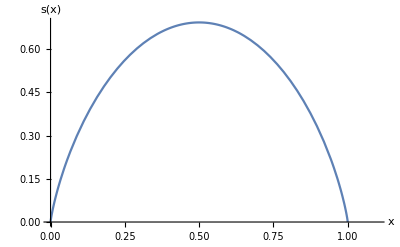

```mathematica
sotx = Plot[ss[x], {x, 0, 1.1}, GridLines->{{{1/2,Red}},None}, GridLinesStyle->Directive[Dashed, Thick], 
AxesLabel->{x, s[x]}]
```

```mathematica
Export["C:\\Users\\Евгений\\Desktop\\github_repos\\notes_7sem\\statphys\\belemuk\\img\\sem2im1.pdf",sotx]
```

C:\Users\Евгений\Desktop\github_repos\notes_7sem\statphys\belemuk\img\sem2im1.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.pdf"]]]
```

```mathematica
MaTeX["x^2"]
```

MaTeX[x^2]